# Predstavitev arhimedskih teles:

PRISEKANI TETRAEDER

Prisekani tetraeder je v geometriji konveksni polieder. Je arhimedsko telo, eno od trinajstih konveksnih izogonalnih neprizmatičnih teles skonstruirano z dvema ali več vrstami pravilnih mnogokotniških stranskih ploskev.

Ima 8 pravilnih stranskih ploskev:
	-> 4 enakostranične trikotnike
	-> 4 pravilnih šestkotnikov

Ima 18 robov in 12 oglišč.

Površina in prostornina:   -Graphics-

```mathematica
Graphics3D[{
Green,Opacity[.5],Polygon[{{0.5,0,0},{0,0.85,0},{0.5,1.7,0},{1.5,1.7,0},{2,0.85,0},{1.5,0,0}}],
Green,Opacity[.5],Polygon[{{0.5,0,0},{0,0.3,0.85},{0.5,0.6,1.7},{1.5,0.6,1.7},{2,0.3,0.85},{1.5,0,0}}],
Green,Opacity[.5],Polygon[{{1.5,0.6,1.7}, {1,1.5,1.7},{1.08,1.95,0.8},{1.5,1.7,0},{2,0.85,0},{2,0.3,0.85}}],
Green,Opacity[.5],Polygon[{{0,0.3,0.85},{0,0.85,0},{0.5,1.7,0},{1.08,1.95,0.8}, {1,1.5,1.7},{0.5,0.6,1.7}}],
Red,Polygon[{{2,0.85,0},{2,0.3,0.85}, {1.5,0,0}}],
Red,Polygon[{{0,0.3,0.85},{0,0.85,0},{0.5,0,0}}],
Red,Polygon[{{0.5,0.6,1.7},{1.5,0.6,1.7}, {1,1.5,1.7}}],
Red,Polygon[{{0.5,1.7,0},{1.5,1.7,0}, {1.08,1.95,0.8}}],
Blue,Tube[{{0.5,0,0},{0,0.85,0},{0.5,1.7,0},{1.5,1.7,0},{2,0.85,0},{1.5,0,0},{0.5,0,0}},0.02],
Blue,Tube[{{0.5,0,0},{0,0.3,0.85},{0.5,0.6,1.7},{1.5,0.6,1.7},{2,0.3,0.85},{1.5,0,0},{0.5,0,0}},0.02],
Blue,Tube[{{1.5,0.6,1.7}, {1,1.5,1.7},{1.08,1.95,0.8},{1.5,1.7,0},{2,0.85,0},{2,0.3,0.85},{1.5,0.6,1.7}},0.02],
Blue,Tube[{{0,0.3,0.85},{0,0.85,0},{0.5,1.7,0},{1.08,1.95,0.8}, {1,1.5,1.7},{0.5,0.6,1.7},{0,0.3,0.85}},0.02]
}]
```

-Graphics3D-

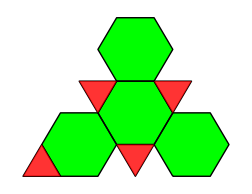

```mathematica
Graphics[{
Green,Polygon[{{3.5,0},{3,0.85},{3.5,1.7},{4.5,1.7},{5,0.85},{4.5,0}}],
Green,Polygon[{{0.5,0},{0,0.85},{0.5,1.7},{1.5,1.7},{2,0.85},{1.5,0}}],
Green,Polygon[{{2,0.85},{3,0.85},{3.5,1.7},{3,2.55},{2,2.55},{1.5,1.7}}],
Green,Polygon[{{2,2.55},{3,2.55},{3.5,3.4},{3,4.25},{2,4.25},{1.5, 3.4}}],
Black,Thick,Line[{{3.5,0},{3,0.85},{3.5,1.7},{4.5,1.7},{5,0.85},{4.5,0},{3.5,0}}],
Black,Line[{{0.5,0},{0,0.85},{0.5,1.7},{1.5,1.7},{2,0.85},{1.5,0},{0.5,0}}],
Black,Line[{{2,0.85},{3,0.85},{3.5,1.7},{3,2.55},{2,2.55},{1.5,1.7},{2,0.85}}],
Black,Line[{{2,2.55},{3,2.55},{3.5,3.4},{3,4.25},{2,4.25},{1.5, 3.4},{2,2.55}}],
Black,Line[{{0, 0.85},{0.5,0},{-0.5,0},{0, 0.85}}],
Black,Line[{{2,0.85},{3,0.85},{2.5,0},{2,0.85}}],
Black,Line[{{2,2.55},{1.5,1.7},{1,2.55},{2,2.55}}],
Black,Line[{{3.5,1.7},{3,2.55},{4,2.55},{3.5,1.7}}],
Red,Opacity[.8],Polygon[{{0, 0.85},{0.5,0},{-0.5,0}}],
Red,Polygon[{{2,0.85},{3,0.85},{2.5,0}}],
Red,Polygon[{{2,2.55},{1.5,1.7},{1,2.55}}],
Red,Polygon[{{3.5,1.7},{3,2.55},{4,2.55}}]
}]
```

KUBOOKTAEDER

Kubooktaeder je v geometriji konveksni polieder. Je arhimedsko telo, eno od trinajstih konveksnih izogonalnih neprizmatičnih teles skonstruirano z dvema ali več vrstami pravilnih mnogokotniških stranskih ploskev.

Ima 14 pravilnih stranskih ploskev:
	-> 8 enakostraničnih trikotnikov 
	-> 6 kvadratov

Ima 24 popolnoma skladnih robov, ki vsak ločuje enakostranični trikotnik od kvadrata.

Ima 12 popolnoma enakih oglišč, v katerih se stikajo dva enakostranična trikotnika in dva kvadrata. Zaradi tega je polpravilni polieder, ki je tako ogliščno kot robovnoprehoden.

Njegov dualni polieder, oziroma Catalanovo telo, je rombski dodekaeder.

Telo je bilo verjetno znano Platonu. V Heronovih Definitiones je naveden Arhimed, ki naj bi izrekel, da je Platon vedel za telo sestavljeno iz 8-ih trikotnikov in 6-ih kvadratov.

Površina in prostornina:  -Graphics-

```mathematica
Graphics3D[{
Green,Opacity[.5],Polygon[{{0,0,0},{0,1,0},{1,1,0},{1,0,0}}],
Green,Opacity[.5],Polygon[{{0,0,1.3},{0,1,1.3},{1,1,1.3},{1,0,1.3}}],
Green,Opacity[.5],Polygon[{{0.5,-0.5,0.65},{1,0,1.3},{1.5,0.5,0.65},{1,0,0}}],
Green,Opacity[.5],Polygon[{{0.5,-0.5,0.65},{0,0,1.3},{-0.5,0.5,0.65},{0,0,0}}],
Green,Opacity[.5],Polygon[{{0.5,1.5,0.65},{1,1,1.3},{1.5,0.5,0.65},{1,1,0}}],
Green,Opacity[.5],Polygon[{{0.5,1.5,0.65},{0,1,1.3},{-0.5,0.5,0.65},{0,1,0}}],
Red,Polygon[{{0,0,0},{1,0,0}, {0.5,-0.5,0.65}}],
Red,Polygon[{{0,0,1.3},{1,0,1.3}, {0.5,-0.5,0.65}}],
Red,Polygon[{{0,1,0},{1,1,0}, {0.5,1.5,0.65}}],
Red,Polygon[{{0,1,1.3},{1,1,1.3}, {0.5,1.5,0.65}}],
Red,Polygon[{{1,1,0},{1,0,0}, {1.5,0.5,0.65}}],
Red,Polygon[{{1,1,1.3},{1,0,1.3}, {1.5,0.5,0.65}}],
Red,Polygon[{{0,1,0},{0,0,0}, {-0.5,0.5,0.65}}],
Red,Polygon[{{0,1,1.3},{0,0,1.3}, {-0.5,0.5,0.65}}],
Blue,Tube[{{0,0,0},{0,1,0},{1,1,0},{1,0,0},{0,0,0}},0.02],
Blue,Tube[{{0,0,1.3},{0,1,1.3},{1,1,1.3},{1,0,1.3},{0,0,1.3}},0.02],
Blue,Tube[{{0.5,-0.5,0.65},{1,0,1.3},{1.5,0.5,0.65},{1,0,0},{0.5,-0.5,0.65}},0.02],
Blue,Tube[{{0.5,-0.5,0.65},{0,0,1.3},{-0.5,0.5,0.65},{0,0,0},{0.5,-0.5,0.65}},0.02],
Blue,Tube[{{0.5,1.5,0.65},{1,1,1.3},{1.5,0.5,0.65},{1,1,0},{0.5,1.5,0.65}},0.02],
Blue,Tube[{{0.5,1.5,0.65},{0,1,1.3},{-0.5,0.5,0.65},{0,1,0},{0.5,1.5,0.65}},0.02],
Red,Opacity[1],Point[{{0,0,0}}]
}]
```

-Graphics3D-

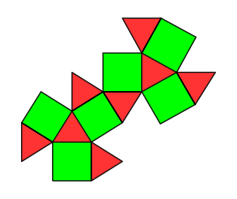

```mathematica
Graphics[{
Green,Polygon[{{0,0},{1,0},{1,1},{0,1}}],
Green,Polygon[{{0,1},{0.5,1.8},{-0.3,2.3},{-0.8,1.5}}],
Green,Polygon[{{1,1},{1.8,1.5},{1.3,2.3},{0.5,1.8}}],
Green,Polygon[{{2.3,2.3},{2.3,3.3},{1.3,3.3},{1.3,2.3}}],
Green,Polygon[{{2.3,2.3},{3.2,2.8},{3.68,1.97},{2.78,1.47}}],
Green,Polygon[{{3.2,2.8},{2.3,3.3},{2.8,4.2},{3.7,3.71}}],
Red,Opacity[.8],Polygon[{{1,1},{0,1},{0.5,1.8}}],
Red,Polygon[{{1,0},{1,1},{1.8,0.5}}],
Red,Polygon[{{0,1},{-0.8,1.5},{-0.8,0.5}}],
Red,Polygon[{{1.3,2.3},{0.5,1.8},{0.5,2.8}}],
Red,Polygon[{{1.8,1.5},{1.3,2.3},{2.3,2.3}}],
Red,Polygon[{{2.3,2.3},{2.3,3.3},{3.2,2.8}}],
Red,Polygon[{{3.2,2.8},{3.68,1.97},{4.2,2.8}}],
Red,Polygon[{{2.3,3.3},{2.8,4.2},{1.8,4.2}}],
Black,Thick,Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
Black,Line[{{0,1},{0.5,1.8},{-0.3,2.3},{-0.8,1.5},{0,1}}],
Black,Line[{{1,1},{1.8,1.5},{1.3,2.3},{0.5,1.8},{1,1}}],
Black,Line[{{2.3,2.3},{2.3,3.3},{1.3,3.3},{1.3,2.3},{2.3,2.3}}],
Black,Line[{{2.3,2.3},{3.2,2.8},{3.68,1.97},{2.78,1.47},{2.3,2.3}}],
Black,Line[{{3.2,2.8},{2.3,3.3},{2.8,4.2},{3.7,3.71},{3.2,2.8}}],
Black,Line[{{1,0},{1,1},{1.8,0.5},{1,0}}],
Black,Line[{{0,1},{-0.8,1.5},{-0.8,0.5},{0,1}}],
Black,Line[{{1.3,2.3},{0.5,1.8},{0.5,2.8},{1.3,2.3}}],
Black,Line[{{1.8,1.5},{1.3,2.3},{2.3,2.3},{1.8,1.5}}],
Black,Line[{{3.2,2.8},{3.68,1.97},{4.2,2.8},{3.2,2.8}}],
Black,Line[{{2.3,3.3},{2.8,4.2},{1.8,4.2},{2.3,3.3}}]
}]
```

PRISEKANA KOCKA(PRISEKANI HEKSAEDER)

... je v geometriji konveksni polieder. Je arhimedsko telo, eno od trinajstih konveksnih izogonalnih neprizmatičnih teles skonstruirano z dvema ali več vrstami pravilnih mnogokotniških stranskih ploskev.

Ima 14 pravilnih stranskih ploskev:
	-> 8 enakostraničnih trikotnikov 
	-> 6 pravilnih osemkotnikovh

Ima 36 robov in 24 oglišč.

Površina in prostornina:  -Graphics-

```mathematica
Graphics3D[{
Green,Opacity[.5],Polygon[{{1,0,0},{0,1,0},{0,2,0},{1,3,0},{2,3,0},{3,2,0},{3,1,0},{2,0,0}}],
Green,Polygon[{{1,0,3},{0,1,3},{0,2,3},{1,3,3},{2,3,3},{3,2,3},{3,1,3},{2,0,3}}],
Green,Polygon[{{3,0,2},{3,1,3},{3,2,3},{3,3,2},{3,3,1},{3,2,0},{3,1,0},{3,0,1}}],
Green,Polygon[{{0,0,2},{0,1,3},{0,2,3},{0,3,2},{0,3,1},{0,2,0},{0,1,0},{0,0,1}}],
Green,Polygon[{{1,0,0},{0,0,1},{0,0,2},{1,0,3},{2,0,3},{3,0,2},{3,0,1},{2,0,0}}],
Green,Polygon[{{1,3,0},{0,3,1},{0,3,2},{1,3,3},{2,3,3},{3,3,2},{3,3,1},{2,3,0}}], 
Blue,Tube[{{1,0,0},{0,1,0},{0,2,0},{1,3,0},{2,3,0},{3,2,0},{3,1,0},{2,0,0},{1,0,0}},0.02],
Blue,Tube[{{1,0,3},{0,1,3},{0,2,3},{1,3,3},{2,3,3},{3,2,3},{3,1,3},{2,0,3},{1,0,3}},0.02],
Blue,Tube[{{3,0,2},{3,1,3},{3,2,3},{3,3,2},{3,3,1},{3,2,0},{3,1,0},{3,0,1},{3,0,2}},0.02],
Blue,Tube[{{0,0,2},{0,1,3},{0,2,3},{0,3,2},{0,3,1},{0,2,0},{0,1,0},{0,0,1},{0,0,2}},0.02],
Blue,Tube[{{1,0,0},{0,0,1},{0,0,2},{1,0,3},{2,0,3},{3,0,2},{3,0,1},{2,0,0},{1,0,0}},0.02],
Blue,Tube[{{1,3,0},{0,3,1},{0,3,2},{1,3,3},{2,3,3},{3,3,2},{3,3,1},{2,3,0},{1,3,0}},0.02],
Red,Polygon[{{1,3,0},{0,3,1}, {0,2,0}}],
Red,Polygon[{{2,3,0},{3,3,1}, {3,2,0}}],
Red,Polygon[{{1,0,0},{0,0,1}, {0,1,0}}],
Red,Polygon[{{2,0,0},{3,0,1}, {3,1,0}}],
Red,Polygon[{{2,0,3},{3,0,2}, {3,1,3}}],
Red,Polygon[{{2,3,3},{3,3,2}, {3,2,3}}],
Red,Polygon[{{1,3,3},{0,3,2}, {0,2,3}}],
Red,Polygon[{{1,0,3},{0,0,2}, {0,1,3}}]
}]
```

-Graphics3D-

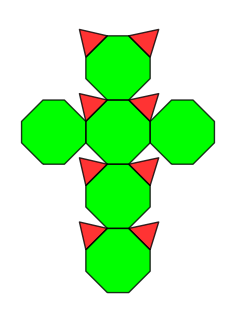

```mathematica
Graphics[{
Green,Polygon[{{1,0},{0,1},{0,2},{1,3},{2,3},{3,2},{3,1},{2,0}}],
Green,Polygon[{{1,3},{0,4},{0,5},{1,6},{2,6},{3,5},{3,4},{2,3}}],
Green,Polygon[{{1,6},{0,7},{0,8},{1,9},{2,9},{3,8},{3,7},{2,6}}],
Green,Polygon[{{1,9},{0,10},{0,11},{1,12},{2,12},{3,11},{3,10},{2,9}}],
Green,Polygon[{{-2,6},{-3,7},{-3,8},{-2,9},{-1,9},{0,8},{0,7},{-1,6}}],
Green,Polygon[{{4,6},{3,7},{3,8},{4,9},{5,9},{6,8},{6,7},{5,6}}],
Red,Opacity[0.8],Polygon[{{0,2},{1,3}, {-0.3,3.3}}],
Red,Opacity[0.8],Polygon[{{3,2},{2,3}, {3.4,3.3}}],
Red,Opacity[0.8],Polygon[{{0,5},{1,6}, {-0.3,6.3}}],
Red,Opacity[0.8],Polygon[{{3,5},{2,6}, {3.4,6.3}}],
Red,Opacity[0.8],Polygon[{{0,8},{1,9}, {-0.3,9.3}}],
Red,Opacity[0.8],Polygon[{{3,8},{2,9}, {3.4,9.3}}],
Red,Opacity[0.8],Polygon[{{0,11},{1,12}, {-0.3,12.3}}],
Red,Opacity[0.8],Polygon[{{3,11},{2,12}, {3.4,12.3}}],
Black,Thick,Line[{{1,0},{0,1},{0,2},{1,3},{2,3},{3,2},{3,1},{2,0},{1,0}}],
Black,Line[{{1,3},{0,4},{0,5},{1,6},{2,6},{3,5},{3,4},{2,3},{1,3}}],
Black,Line[{{1,6},{0,7},{0,8},{1,9},{2,9},{3,8},{3,7},{2,6},{1,6}}],
Black,Line[{{1,9},{0,10},{0,11},{1,12},{2,12},{3,11},{3,10},{2,9},{1,9}}],
Black,Line[{{-2,6},{-3,7},{-3,8},{-2,9},{-1,9},{0,8},{0,7},{-1,6},{-2,6}}],
Black,Line[{{4,6},{3,7},{3,8},{4,9},{5,9},{6,8},{6,7},{5,6},{4,6}}],
Black,Line[{{0,2},{1,3}, {-0.3,3.3},{0,2}}],
Black,Line[{{3,2},{2,3}, {3.4,3.3},{3,2}}],
Black,Line[{{0,5},{1,6}, {-0.3,6.3},{0,5}}],
Black,Line[{{3,5},{2,6}, {3.4,6.3},{3,5}}],
Black,Line[{{0,8},{1,9}, {-0.3,9.3},{0,8}}],
Black,Line[{{3,8},{2,9}, {3.4,9.3},{3,8}}],
Black,Line[{{0,11},{1,12}, {-0.3,12.3},{0,11}}],
Black,Line[{{3,11},{2,12}, {3.4,12.3},{3,11}}]
}]
```

ROMBIKUBOOKTAEDER

... je v geometriji konveksni polieder. Je arhimedsko telo, eno od trinajstih konveksnih izogonalnih neprizmatičnih teles skonstruirano z dvema ali več vrstami pravilnih mnogokotniških stranskih ploskev.

Ima 26 pravilnih stranskih ploskev:
	-> 8 enakostraničnih trikotnikov
	-> 18 kvadratov

Ima 48 robov in 24 oglišč.

Površina in prostornina:  -Graphics-

```mathematica
Graphics3D[{
Green,Opacity[.5],Polygon[{{0.7,0.7,0},{0.7,1.7,0},{1.7,1.7,0},{1.7,0.7,0}}],
Green,Polygon[{{0.7,0.7,2.5},{0.7,1.7,2.5},{1.7,1.7,2.5},{1.7,0.7,2.5}}],
Green,Polygon[{{0.7,2.5,0.7},{0.7,2.5,1.7},{1.7,2.5,1.7},{1.7,2.5,0.7}}],
Green,Polygon[{{1.7,0,0.7},{1.7,0,1.7},{0.7,0,1.7},{0.7,0,0.7}}],
Green,Polygon[{{0,0.7,0.7},{0,0.7,1.7},{0,1.7,1.7},{0,1.7,0.7}}],
Green,Polygon[{{2.5,0.7,0.7},{2.5,0.7,1.7},{2.5,1.7,1.7},{2.5,1.7,0.7}}],
Green,Polygon[{{1.7,0.7,2.5},{2.5,0.7,1.7},{2.5,1.7,1.7},{1.7,1.7,2.5}}],
Green,Polygon[{{0.7,0.7,2.5},{0,0.7,1.7},{0,1.7,1.7},{0.7,1.7,2.5}}],
Green,Polygon[{{0.7,0.7,0},{0,0.7,0.7},{0,1.7,0.7},{0.7,1.7,0}}],
Green,Polygon[{{1.7,0.7,0},{2.5,0.7,0.7},{2.5,1.7,0.7},{1.7,1.7,0}}],
Green,Polygon[{{0.7,0.7,2.5},{0.7,0,1.7},{1.7,0,1.7},{1.7,0.7,2.5}}],
Green,Polygon[{{0.7,0.7,0},{0.7,0,0.7},{1.7,0,0.7},{1.7,0.7,0}}],
Green,Polygon[{{0.7,1.7,0},{0.7,2.5,0.7},{1.7,2.5,0.7},{1.7,1.7,0}}],
Green,Polygon[{{0.7,1.7,2.5},{0.7,2.5,1.7},{1.7,2.5,1.7},{1.7,1.7,2.5}}],
Green,Polygon[{{0,0.7,0.7},{0,0.7,1.7},{0.7,0,1.7},{0.7,0,0.7}}],
Green,Polygon[{{2.5,0.7,0.7},{2.5,0.7,1.7},{1.7,0,1.7},{1.7,0,0.7}}],
Green,Polygon[{{2.5,1.7,0.7},{2.5,1.7,1.7},{1.7,2.5,1.7},{1.7,2.5,0.7}}],
Green,Polygon[{{0,1.7,0.7},{0,1.7,1.7},{0.7,2.5,1.7},{0.7,2.5,0.7}}],
Red,Polygon[{{0.7,1.7,2.5},{0,1.7,1.7},{0.7,2.5,1.7}}],
Red,Polygon[{{0.7,1.7,0},{0,1.7,0.7},{0.7,2.5,0.7}}],
Red,Polygon[{{1.7,1.7,0},{2.5,1.7,0.7},{1.7,2.5,0.7}}],
Red,Polygon[{{1.7,1.7,2.5},{2.5,1.7,1.7},{1.7,2.5,1.7}}],
Red,Polygon[{{1.7,0.7,2.5},{2.5,0.7,1.7},{1.7,0,1.7}}],
Red,Polygon[{{1.7,0.7,0},{2.5,0.7,0.7},{1.7,0,0.7}}],
Red,Polygon[{{0.7,0.7,0},{0,0.7,0.7},{0.7,0,0.7}}],
Red,Polygon[{{0.7,0.7,2.5},{0,0.7,1.7},{0.7,0,1.7}}],
Blue,Opacity[1],Tube[{{0.7,0.7,0},{0.7,1.7,0},{1.7,1.7,0},{1.7,0.7,0},{0.7,0.7,0}},0.02],
Blue,Tube[{{0.7,0.7,2.5},{0.7,1.7,2.5},{1.7,1.7,2.5},{1.7,0.7,2.5},{0.7,0.7,2.5}},0.02],
Blue,Tube[{{0.7,2.5,0.7},{0.7,2.5,1.7},{1.7,2.5,1.7},{1.7,2.5,0.7},{0.7,2.5,0.7}},0.02],
Blue,Tube[{{1.7,0,0.7},{1.7,0,1.7},{0.7,0,1.7},{0.7,0,0.7},{1.7,0,0.7}},0.02],
Blue,Tube[{{0,0.7,0.7},{0,0.7,1.7},{0,1.7,1.7},{0,1.7,0.7},{0,0.7,0.7}},0.02],
Blue,Tube[{{2.5,0.7,0.7},{2.5,0.7,1.7},{2.5,1.7,1.7},{2.5,1.7,0.7},{2.5,0.7,0.7}},0.02],
Blue,Tube[{{0.7,1.7,2.5},{0,1.7,1.7},{0.7,2.5,1.7},{0.7,1.7,2.5}},0.02],
Blue,Tube[{{0.7,1.7,0},{0,1.7,0.7},{0.7,2.5,0.7},{0.7,1.7,0}},0.02],
Blue,Tube[{{1.7,1.7,0},{2.5,1.7,0.7},{1.7,2.5,0.7},{1.7,1.7,0}},0.02],
Blue,Tube[{{1.7,1.7,2.5},{2.5,1.7,1.7},{1.7,2.5,1.7},{1.7,1.7,2.5}},0.02],
Blue,Tube[{{1.7,0.7,2.5},{2.5,0.7,1.7},{1.7,0,1.7},{1.7,0.7,2.5}},0.02],
Blue,Tube[{{1.7,0.7,0},{2.5,0.7,0.7},{1.7,0,0.7},{1.7,0.7,0}},0.02],
Blue,Tube[{{0.7,0.7,0},{0,0.7,0.7},{0.7,0,0.7},{0.7,0.7,0}},0.02],
Blue,Tube[{{0.7,0.7,2.5},{0,0.7,1.7},{0.7,0,1.7},{0.7,0.7,2.5}},0.02]
}]
```

-Graphics3D-

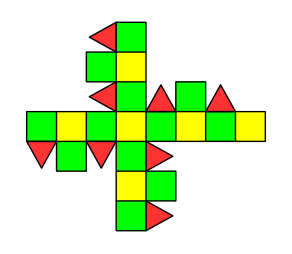

```mathematica
Graphics[{
Yellow,Polygon[{{0,0},{1,0},{1,1},{0,1}}],
Green,Polygon[{{0,1},{1,1},{1,2},{0,2}}],
Yellow,Polygon[{{0,2},{1,2},{1,3},{0,3}}],
Green,Polygon[{{0,3},{1,3},{1,4},{0,4}}],
Green,Polygon[{{0,-1},{1,-1},{1,0},{0,0}}],
Yellow,Polygon[{{0,-2},{1,-2},{1,-1},{0,-1}}],
Green,Polygon[{{0,-3},{1,-3},{1,-2},{0,-2}}],
Green,Polygon[{{-1,2},{0,2},{0,3},{-1,3}}],
Green,Polygon[{{1,-2},{2,-2},{2,-1},{1,-1}}],
Green,Polygon[{{-1,0},{0,0},{0,1},{-1,1}}],
Yellow,Polygon[{{-2,0},{-1,0},{-1,1},{-2,1}}],
Green,Polygon[{{-2,-1},{-1,-1},{-1,0},{-2,0}}],
Green,Polygon[{{-3,0},{-2,0},{-2,1},{-3,1}}],
Green,Polygon[{{1,0},{2,0},{2,1},{1,1}}],
Yellow,Polygon[{{2,0},{3,0},{3,1},{2,1}}],
Green,Polygon[{{3,0},{4,0},{4,1},{3,1}}],
Yellow,Polygon[{{4,0},{5,0},{5,1},{4,1}}],
Green,Polygon[{{2,1},{3,1},{3,2},{2,2}}],
Red,Opacity[0.8],Polygon[{{0,1},{0,2},{-0.9,1.5}}],
Red,Polygon[{{0,3},{0,4},{-0.9,3.5}}],
Red,Polygon[{{0,0},{-1,0},{-0.5,-0.9}}],
Red,Polygon[{{-2,0},{-3,0},{-2.5,-0.9}}],
Red,Polygon[{{1,0},{1,-1},{1.9,-0.5}}],
Red,Polygon[{{1,-2},{1,-3},{1.9,-2.5}}],
Red,Polygon[{{1,1},{2,1},{1.5,1.9}}],
Red,Polygon[{{3,1},{4,1},{3.5,1.9}}],
Black,Opacity[1],Thick,Line[{{0,1},{1,1},{1,2},{0,2},{0,1}}],
Black,Thick,Line[{{0,3},{1,3},{1,4},{0,4},{0,3}}],
Black,Thick,Line[{{0,-1},{1,-1},{1,0},{0,0},{0,-1}}],
Black,Thick,Line[{{0,-3},{1,-3},{1,-2},{0,-2},{0,-3}}],
Black,Thick,Line[{{-1,2},{0,2},{0,3},{-1,3},{-1,2}}],
Black,Thick,Line[{{1,-2},{2,-2},{2,-1},{1,-1},{1,-2}}],
Black,Thick,Line[{{-1,0},{0,0},{0,1},{-1,1},{-1,0}}],
Black,Thick,Line[{{-2,-1},{-1,-1},{-1,0},{-2,0},{-2,-1}}],
Black,Thick,Line[{{-3,0},{-2,0},{-2,1},{-3,1},{-3,0}}],
Black,Thick,Line[{{1,0},{2,0},{2,1},{1,1},{1,0}}],
Black,Thick,Line[{{3,0},{4,0},{4,1},{3,1},{3,0}}],
Black,Thick,Line[{{2,1},{3,1},{3,2},{2,2},{2,1}}],
Black,Thick,Line[{{1,2},{1,3}}],
Black,Thick,Line[{{-1,1},{-2,1}}],
Black,Thick,Line[{{0,-1},{0,-2}}],
Black,Thick,Line[{{2,0},{3,0}}],
Black,Thick,Line[{{4,0},{5,0},{5,1},{4,1}}],
Black,Thick,Line[{{0,1},{0,2},{-0.9,1.5},{0,1}}],
Black,Thick,Line[{{0,3},{0,4},{-0.9,3.5},{0,3}}],
Black,Thick,Line[{{0,0},{-1,0},{-0.5,-0.9},{0,0}}],
Black,Thick,Line[{{-2,0},{-3,0},{-2.5,-0.9},{-2,0}}],
Black,Thick,Line[{{1,0},{1,-1},{1.9,-0.5},{1,0}}],
Black,Thick,Line[{{1,-2},{1,-3},{1.9,-2.5},{1,-2}}],
Black,Thick,Line[{{1,1},{2,1},{1.5,1.9},{1,1}}],
Black,Thick,Line[{{3,1},{4,1},{3.5,1.9},{3,1}}]
}]
```

PRISEKANI OKTAEDER

Prisekani oktaeder je v geometriji konveksni polieder. Je arhimedsko telo, eno od trinajstih konveksnih izogonalnih neprizmatičnih teles skonstruirano z dvema ali več vrstami pravilnih mnogokotniških stranskih ploskev.

Ima 14 pravilnih stranskih ploskev: 
	-> 6 kvadratov 
	-> 8 šestkonikov 

Ima 36 robov in 24 oglišč. 

Vsaka izmed stranskih ploskev ima točkovno simetrijo in je tako prisekani oktaeder ali zonoeder.

Površina in prostornina:  -Graphics-

```mathematica
Graphics3D[{
Green,Opacity[.5],Polygon[{{0.5,0,0},{0,1,0},{0.5,2,0},{1.5,2,0},{2,1,0},{1.5,0,0}}],
Green,Polygon[{{0.5,0,2.8},{0,1,2.8},{0.5,2,2.8},{1.5,2,2.8},{2,1,2.8},{1.5,0,2.8}}],
Green,Polygon[{{0.5,0,2.8},{0,-0.35,1.8},{0.5,-0.7,0.8},{1.5,-0.7,0.8},{2,-0.35,1.8},{1.5,0,2.8}}],
Green,Polygon[{{0.5,2.7,2},{0,2.35,1},{0.5,2,0},{1.5,2,0},{2,2.35,1},{1.5,2.7,2}}],
Green,Polygon[{{1.5,-0.7,0.8},{2,-0.35,1.8},{2.46,0.6,1.8},{2.52,1.33,0.96},{2,1,0},{1.5,0,0}}],
Green,Polygon[{{0.5,-0.7,0.8},{0,-0.35,1.8},{-0.48,0.6,1.8},{-0.52,1.33,0.97},{0,1,0},{0.5,0,0}}],
Green,Polygon[{{2.46,0.6,1.8},{2,1,2.8},{1.5,2,2.8},{1.5,2.7,2},{2,2.35,1},{2.52,1.33,0.96}}],
Green,Polygon[{{-0.48,0.6,1.8},{0,1,2.8},{0.5,2,2.8},{0.5,2.7,2},{0,2.35,1},{-0.52,1.33,0.97}}],
Red,Polygon[{{0.5,-0.7,0.8},{0.5,0,0},{1.5,0,0},{1.5,-0.7,0.8}}],
Red,Polygon[{{0.5,2,2.8},{0.5,2.7,2},{1.5,2.7,2},{1.5,2,2.8}}],
Red,Polygon[{{1.5,0,2.8},{2,-0.35,1.8},{2.46,0.6,1.8},{2,1,2.8}}],
Red,Polygon[{{0.5,0,2.8},{0,-0.35,1.8},{-0.48,0.6,1.8},{0,1,2.8}}],
Red,Polygon[{{2.52,1.33,0.96},{2,1,0},{1.5,2,0},{2,2.35,1}}],
Red,Opacity[.5],Polygon[{{0,1,0},{0.5,2,0},{0,2.35,1},{-0.52,1.33,0.97}}],
Blue,Opacity[1],Tube[{{0.5,0,0},{0,1,0},{0.5,2,0},{1.5,2,0},{2,1,0},{1.5,0,0},{0.5,0,0}},0.02],
Blue,Tube[{{0.5,0,2.8},{0,1,2.8},{0.5,2,2.8},{1.5,2,2.8},{2,1,2.8},{1.5,0,2.8},{0.5,0,2.8}},0.02],
Blue,Tube[{{0.5,0,2.8},{0,-0.35,1.8},{0.5,-0.7,0.8},{1.5,-0.7,0.8},{2,-0.35,1.8},{1.5,0,2.8},{0.5,0,2.8}},0.02],
Blue,Tube[{{0.5,2.7,2},{0,2.35,1},{0.5,2,0},{1.5,2,0},{2,2.35,1},{1.5,2.7,2},{0.5,2.7,2}},0.02],
Blue,Tube[{{1.5,-0.7,0.8},{2,-0.35,1.8},{2.46,0.6,1.8},{2.52,1.33,0.96},{2,1,0},{1.5,0,0},{1.5,-0.7,0.8}},0.02],
Blue,Tube[{{0.5,-0.7,0.8},{0,-0.35,1.8},{-0.48,0.6,1.8},{-0.52,1.33,0.97},{0,1,0},{0.5,0,0},{0.5,-0.7,0.8}},0.02],
Blue,Tube[{{2.46,0.6,1.8},{2,1,2.8},{1.5,2,2.8},{1.5,2.7,2},{2,2.35,1},{2.52,1.33,0.96},{2.46,0.6,1.8}},0.02],
Blue,Tube[{{-0.48,0.6,1.8},{0,1,2.8},{0.5,2,2.8},{0.5,2.7,2},{0,2.35,1},{-0.52,1.33,0.97},{-0.48,0.6,1.8}},0.02]
}]
```

-Graphics3D-

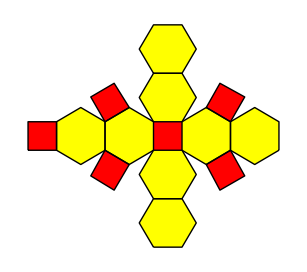

```mathematica
Graphics[{
Yellow,Polygon[{{0.5,0},{0,0.85},{0.5,1.7},{1.5,1.7},{2,0.85},{1.5,0}}],
Yellow,Polygon[{{0.5,1.7},{0,2.55},{0.5,3.4},{1.5,3.4},{2,2.55},{1.5,1.7}}],
Yellow,Polygon[{{0.5,4.4},{0,5.25},{0.5,6.1},{1.5,6.1},{2,5.25},{1.5,4.4}}],
Yellow,Polygon[{{0.5,6.1},{0,6.95},{0.5,7.8},{1.5,7.8},{2,6.95},{1.5,6.1}}],
Yellow,Polygon[{{0.5,3.4},{0.5,4.4},{-0.35,4.9},{-1.2,4.4},{-1.2,3.4},{-0.35,2.9}}],
Yellow,Polygon[{{-1.2,3.4},{-1.2,4.4},{-2.05,4.9},{-2.9,4.4},{-2.9,3.4},{-2.05,2.9}}],
Yellow,Polygon[{{3.2,3.4},{3.2,4.4},{2.35,4.9},{1.5,4.4},{1.5,3.4},{2.35,2.9}}],
Yellow,Polygon[{{4.9,3.4},{4.9,4.4},{4.05,4.9},{3.2,4.4},{3.2,3.4},{4.05,2.9}}],
Red,Polygon[{{0.5,3.4},{1.5,3.4},{1.5,4.4},{0.5,4.4}}],
Red,Polygon[{{-3.9,3.4},{-2.9,3.4},{-2.9,4.4},{-3.9,4.4}}],
Red,Polygon[{{-0.35,4.9},{-1.2,4.4},{-1.7,5.27},{-0.88,5.75}}],
Red,Polygon[{{-0.35,2.9},{-1.2,3.4},{-1.7,2.5},{-0.88,2}}],
Red,Polygon[{{2.35,4.9},{3.2,4.4},{3.7,5.27},{2.83,5.75}}],
Red,Polygon[{{2.35,2.9},{3.2,3.4},{3.7,2.5},{2.83,2}}],
Black,Opacity[1],Thick,Line[{{0.5,0},{0,0.85},{0.5,1.7},{1.5,1.7},{2,0.85},{1.5,0},{0.5,0}}],
Black,Thick,Line[{{0.5,1.7},{0,2.55},{0.5,3.4},{1.5,3.4},{2,2.55},{1.5,1.7},{0.5,1.7}}],
Black,Thick,Line[{{0.5,4.4},{0,5.25},{0.5,6.1},{1.5,6.1},{2,5.25},{1.5,4.4},{0.5,4.4}}],
Black,Thick,Line[{{0.5,6.1},{0,6.95},{0.5,7.8},{1.5,7.8},{2,6.95},{1.5,6.1},{0.5,6.1}}],
Black,Thick,Line[{{0.5,3.4},{0.5,4.4},{-0.35,4.9},{-1.2,4.4},{-1.2,3.4},{-0.35,2.9},{0.5,3.4}}],
Black,Thick,Line[{{-1.2,3.4},{-1.2,4.4},{-2.05,4.9},{-2.9,4.4},{-2.9,3.4},{-2.05,2.9},{-1.2,3.4}}],
Black,Thick,Line[{{3.2,3.4},{3.2,4.4},{2.35,4.9},{1.5,4.4},{1.5,3.4},{2.35,2.9},{3.2,3.4}}],
Black,Thick,Line[{{4.9,3.4},{4.9,4.4},{4.05,4.9},{3.2,4.4},{3.2,3.4},{4.05,2.9},{4.9,3.4}}],
Black,Thick,Line[{{-3.9,3.4},{-2.9,3.4},{-2.9,4.4},{-3.9,4.4},{-3.9,3.4}}],
Black,Thick,Line[{{-0.35,4.9},{-1.2,4.4},{-1.7,5.27},{-0.88,5.75},{-0.35,4.9}}],
Black,Thick,Line[{{-0.35,2.9},{-1.2,3.4},{-1.7,2.5},{-0.88,2},{-0.35,2.9}}],
Black,Thick,Line[{{2.35,4.9},{3.2,4.4},{3.7,5.27},{2.83,5.75},{2.35,4.9}}],
Black,Thick,Line[{{2.35,2.9},{3.2,3.4},{3.7,2.5},{2.83,2},{2.35,2.9}}],
}]
```

PRISEKANI KUBOOKTAEDER

Prisekani kubooktaeder je v geometriji konveksni polieder. Je arhimedsko telo, eno od trinajstih konveksnih izogonalnih neprizmatičnih teles skonstruirano z dvema ali več vrstami pravilnih mnogokotniških stranskih ploskev.

Ima 26 pravilnih stranskih ploskev:
	-> 12 kvadratov
	-> 8 pravilnih šestkotnikov
	-> 6 osemkotnikov 

Ima 72 robov in 48 oglišč. 

Ker ima vsaka stranska ploskev točkovno simetrijo, kar je enakovredno vrtilni simetriji, je to telo tudi zonoeder.

Površina in prostornina:  -Graphics-

```mathematica
Graphics3D[{
Green,Opacity[.5],Polygon[{{2,1,0},{1,2,0},{1,3,0},{2,4,0},{3,4,0},{4,3,0},{4,2,0},{3,1,0}}],
Green,Polygon[{{2,1,5},{1,2,5},{1,3,5},{2,4,5},{3,4,5},{4,3,5},{4,2,5},{3,1,5}}],
Green,Polygon[{{5,1,3},{5,2,4},{5,3,4},{5,4,3},{5,4,2},{5,3,1},{5,2,1},{5,1,2}}],
Green,Polygon[{{0,1,3},{0,2,4},{0,3,4},{0,4,3},{0,4,2},{0,3,1},{0,2,1},{0,1,2}}],
Green,Polygon[{{2,0,1},{1,0,2},{1,0,3},{2,0,4},{3,0,4},{4,0,3},{4,0,2},{3,0,1}}],
Green,Polygon[{{2,5,1},{1,5,2},{1,5,3},{2,5,4},{3,5,4},{4,5,3},{4,5,2},{3,5,1}}],
Red,Polygon[{{2,0,1},{2,1,0},{3,1,0},{3,0,1}}],
Red,Polygon[{{2,5,1},{2,4,0},{3,4,0},{3,5,1}}],
Red,Polygon[{{2,0,4},{2,1,5},{3,1,5},{3,0,4}}],
Red,Polygon[{{2,5,4},{2,4,5},{3,4,5},{3,5,4}}],
Red,Polygon[{{5,2,1},{4,2,0},{4,3,0},{5,3,1}}],
Red,Polygon[{{5,2,4},{4,2,5},{4,3,5},{5,3,4}}],
Red,Polygon[{{0,2,1},{1,2,0},{1,3,0},{0,3,1}}],
Red,Polygon[{{0,2,4},{1,2,5},{1,3,5},{0,3,4}}],
Red,Polygon[{{4,0,2},{4,0,3},{5,1,3},{5,1,2}}],
Red,Polygon[{{1,0,2},{1,0,3},{0,1,3},{0,1,2}}],
Red,Polygon[{{4,5,2},{4,5,3},{5,4,3},{5,4,2}}],
Red,Polygon[{{1,5,2},{1,5,3},{0,4,3},{0,4,2}}],
Yellow,Opacity[0.6],Polygon[{{4,2,0},{3,1,0},{3,0,1},{4,0,2},{5,1,2},{5,2,1}}],
Yellow,Polygon[{{4,2,5},{3,1,5},{3,0,4},{4,0,3},{5,1,3},{5,2,4}}],
Yellow,Polygon[{{1,2,0},{2,1,0},{2,0,1},{1,0,2},{0,1,2},{0,2,1}}],
Yellow,Polygon[{{1,2,5},{2,1,5},{2,0,4},{1,0,3},{0,1,3},{0,2,4}}],
Yellow,Polygon[{{4,3,0},{3,4,0},{3,5,1},{4,5,2},{5,4,2},{5,3,1}}],
Yellow,Polygon[{{4,3,5},{3,4,5},{3,5,4},{4,5,3},{5,4,3},{5,3,4}}],
Yellow,Polygon[{{1,3,0},{2,4,0},{2,5,1},{1,5,2},{0,4,2},{0,3,1}}],
Yellow,Polygon[{{1,3,5},{2,4,5},{2,5,4},{1,5,3},{0,4,3},{0,3,4}}],
Blue,Opacity[1],Tube[{{2,1,0},{1,2,0},{1,3,0},{2,4,0},{3,4,0},{4,3,0},{4,2,0},{3,1,0},{2,1,0}},0.02],
Blue,Tube[{{2,1,5},{1,2,5},{1,3,5},{2,4,5},{3,4,5},{4,3,5},{4,2,5},{3,1,5},{2,1,5}},0.02],
Blue,Tube[{{5,1,3},{5,2,4},{5,3,4},{5,4,3},{5,4,2},{5,3,1},{5,2,1},{5,1,2},{5,1,3}},0.02],
Blue,Tube[{{0,1,3},{0,2,4},{0,3,4},{0,4,3},{0,4,2},{0,3,1},{0,2,1},{0,1,2},{0,1,3}},0.02],
Blue,Tube[{{2,0,1},{1,0,2},{1,0,3},{2,0,4},{3,0,4},{4,0,3},{4,0,2},{3,0,1},{2,0,1}},0.02],
Blue,Tube[{{2,5,1},{1,5,2},{1,5,3},{2,5,4},{3,5,4},{4,5,3},{4,5,2},{3,5,1},{2,5,1}},0.02],
Blue,Tube[{{4,2,0},{3,1,0},{3,0,1},{4,0,2},{5,1,2},{5,2,1},{4,2,0}},0.02],
Blue,Tube[{{4,2,5},{3,1,5},{3,0,4},{4,0,3},{5,1,3},{5,2,4},{4,2,5}},0.02],
Blue,Tube[{{1,2,0},{2,1,0},{2,0,1},{1,0,2},{0,1,2},{0,2,1},{1,2,0}},0.02],
Blue,Tube[{{1,2,5},{2,1,5},{2,0,4},{1,0,3},{0,1,3},{0,2,4},{1,2,5}},0.02],
Blue,Tube[{{4,3,0},{3,4,0},{3,5,1},{4,5,2},{5,4,2},{5,3,1},{4,3,0}},0.02],
Blue,Tube[{{4,3,5},{3,4,5},{3,5,4},{4,5,3},{5,4,3},{5,3,4},{4,3,5}},0.02],
Blue,Tube[{{1,3,0},{2,4,0},{2,5,1},{1,5,2},{0,4,2},{0,3,1},{1,3,0}},0.02],
Blue,Tube[{{1,3,5},{2,4,5},{2,5,4},{1,5,3},{0,4,3},{0,3,4},{1,3,5}},0.02]
}]
```

-Graphics3D-

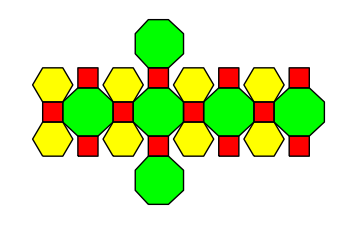

```mathematica
Graphics[{
Yellow,Polygon[{{0.5,0},{0,0.85},{0.5,1.7},{1.5,1.7},{2,0.85},{1.5,0}}],
Yellow,Polygon[{{0.5,2.7},{0,3.55},{0.5,4.4},{1.5,4.4},{2,3.55},{1.5,2.7}}],
Yellow,Polygon[{{4,0},{3.5,0.85},{4,1.7},{5,1.7},{5.5,0.85},{5,0}}],
Yellow,Polygon[{{4,2.7},{3.5,3.55},{4,4.4},{5,4.4},{5.5,3.55},{5,2.7}}],
Yellow,Polygon[{{7.5,0},{7,0.85},{7.5,1.7},{8.5,1.7},{9,0.85},{8.5,0}}],
Yellow,Polygon[{{7.5,2.7},{7,3.55},{7.5,4.4},{8.5,4.4},{9,3.55},{8.5,2.7}}],
Yellow,Polygon[{{11,0},{10.5,0.85},{11,1.7},{12,1.7},{12.5,0.85},{12,0}}],
Yellow,Polygon[{{11,2.7},{10.5,3.55},{11,4.4},{12,4.4},{12.5,3.55},{12,2.7}}],
Red, Polygon[{{0.5,1.7},{1.5,1.7},{1.5,2.7},{0.5,2.7}}],
Red, Polygon[{{4,1.7},{5,1.7},{5,2.7},{4,2.7}}],
Red, Polygon[{{7.5,1.7},{8.5,1.7},{8.5,2.7},{7.5,2.7}}],
Red, Polygon[{{11,1.7},{12,1.7},{12,2.7},{11,2.7}}],
Red, Polygon[{{2.25,0},{3.25,0},{3.25,1},{2.25,1}}],
Red, Polygon[{{2.25,3.4},{3.25,3.4},{3.25,4.4},{2.25,4.4}}],
Red, Polygon[{{5.75,0},{6.75,0},{6.75,1},{5.75,1}}],
Red, Polygon[{{5.75,3.4},{6.75,3.4},{6.75,4.4},{5.75,4.4}}],
Red, Polygon[{{9.25,0},{10.25,0},{10.25,1},{9.25,1}}],
Red, Polygon[{{9.25,3.4},{10.25,3.4},{10.25,4.4},{9.25,4.4}}],
Red, Polygon[{{12.75,0},{13.75,0},{13.75,1},{12.75,1}}],
Red, Polygon[{{12.75,3.4},{13.75,3.4},{13.75,4.4},{12.75,4.4}}],
Green,Polygon[{{1.5,2.7},{1.5,1.7},{2.25,1},{3.25,1},{4,1.7},{4,2.7},{3.25,3.4},{2.25,3.4}}],
Green,Polygon[{{5,2.7},{5,1.7},{5.75,1},{6.75,1},{7.5,1.7},{7.5,2.7},{6.75,3.4},{5.75,3.4}}],
Green,Polygon[{{8.5,2.7},{8.5,1.7},{9.25,1},{10.25,1},{11,1.7},{11,2.7},{10.25,3.4},{9.25,3.4}}],
Green,Polygon[{{12,2.7},{12,1.7},{12.75,1},{13.75,1},{14.5,1.7},{14.5,2.7},{13.75,3.4},{12.75,3.4}}],
Green,Polygon[{{5.75,4.4},{6.75,4.4},{7.5,5.1},{7.5,6.1},{6.75,6.8},{5.75,6.8},{5.1,6.1},{5.1,5.1}}],
Green,Polygon[{{5.75,-2.4},{6.75,-2.4},{7.5,-1.7},{7.5,-0.7},{6.75,0},{5.75,0},{5.1,-0.7},{5.1,-1.7}}],
Black,Opacity[1],Thick,Line[{{0.5,0},{0,0.85},{0.5,1.7},{1.5,1.7},{2,0.85},{1.5,0},{0.5,0},{0.5,0}}],
Black,Thick,Line[{{0.5,2.7},{0,3.55},{0.5,4.4},{1.5,4.4},{2,3.55},{1.5,2.7},{0.5,2.7}}],
Black,Thick,Line[{{4,0},{3.5,0.85},{4,1.7},{5,1.7},{5.5,0.85},{5,0},{4,0}}],
Black,Thick,Line[{{4,2.7},{3.5,3.55},{4,4.4},{5,4.4},{5.5,3.55},{5,2.7},{4,2.7}}],
Black,Thick,Line[{{7.5,0},{7,0.85},{7.5,1.7},{8.5,1.7},{9,0.85},{8.5,0},{7.5,0}}],
Black,Thick,Line[{{7.5,2.7},{7,3.55},{7.5,4.4},{8.5,4.4},{9,3.55},{8.5,2.7},{7.5,2.7}}],
Black,Thick,Line[{{11,0},{10.5,0.85},{11,1.7},{12,1.7},{12.5,0.85},{12,0},{11,0}}],
Black,Thick,Line[{{11,2.7},{10.5,3.55},{11,4.4},{12,4.4},{12.5,3.55},{12,2.7},{11,2.7}}],
Black,Thick,Line[{{0.5,1.7},{1.5,1.7},{1.5,2.7},{0.5,2.7},{0.5,1.7}}],
Black,Thick,Line[{{4,1.7},{5,1.7},{5,2.7},{4,2.7},{4,1.7}}],
Black,Thick,Line[{{7.5,1.7},{8.5,1.7},{8.5,2.7},{7.5,2.7},{7.5,1.7}}],
Black,Thick,Line[{{11,1.7},{12,1.7},{12,2.7},{11,2.7},{11,1.7}}],
Black,Thick,Line[{{2.25,0},{3.25,0},{3.25,1},{2.25,1},{2.25,0}}],
Black,Thick,Line[{{2.25,3.4},{3.25,3.4},{3.25,4.4},{2.25,4.4},{2.25,3.4}}],
Black,Thick,Line[{{5.75,0},{6.75,0},{6.75,1},{5.75,1},{5.75,0}}],
Black,Thick,Line[{{5.75,3.4},{6.75,3.4},{6.75,4.4},{5.75,4.4},{5.75,3.4}}],
Black,Thick,Line[{{9.25,0},{10.25,0},{10.25,1},{9.25,1},{9.25,0}}],
Black,Thick,Line[{{9.25,3.4},{10.25,3.4},{10.25,4.4},{9.25,4.4},{9.25,3.4}}],
Black,Thick,Line[{{12.75,0},{13.75,0},{13.75,1},{12.75,1},{12.75,0}}],
Black,Thick,Line[{{12.75,3.4},{13.75,3.4},{13.75,4.4},{12.75,4.4},{12.75,3.4}}],
Black,Thick,Line[{{1.5,2.7},{1.5,1.7},{2.25,1},{3.25,1},{4,1.7},{4,2.7},{3.25,3.4},{2.25,3.4},{1.5,2.7}}],
Black,Thick,Line[{{5,2.7},{5,1.7},{5.75,1},{6.75,1},{7.5,1.7},{7.5,2.7},{6.75,3.4},{5.75,3.4},{5,2.7}}],
Black,Thick,Line[{{8.5,2.7},{8.5,1.7},{9.25,1},{10.25,1},{11,1.7},{11,2.7},{10.25,3.4},{9.25,3.4},{8.5,2.7}}],
Black,Thick,Line[{{12,2.7},{12,1.7},{12.75,1},{13.75,1},{14.5,1.7},{14.5,2.7},{13.75,3.4},{12.75,3.4},{12,2.7}}],
Black,Thick,Line[{{5.75,4.4},{6.75,4.4},{7.5,5.1},{7.5,6.1},{6.75,6.8},{5.75,6.8},{5.1,6.1},{5.1,5.1},{5.75,4.4}}],
Black,Thick,Line[{{5.75,-2.4},{6.75,-2.4},{7.5,-1.7},{7.5,-0.7},{6.75,0},{5.75,0},{5.1,-0.7},{5.1,-1.7},{5.75,-2.4}}]
}]
```